```mathematica
SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/Conductivity_ZrC/ZrC_kappaPh_RESULTS/"];
filePerf={"0_noZP/BULK/PERF/t_kappa_31.dat", "10/BULK/PERF/t_kappa_31.dat", "3800/BULK/PERF/t_kappa_31.dat", "PBE10/BULK/PERF/t_kappa_31.dat"};
fileIso={"0_noZP/BULK/ISO/t_kappa_31.dat", "10/BULK/ISO/t_kappa_31.dat", "3800/BULK/ISO/t_kappa_31.dat", "PBE10/BULK/ISO/t_kappa_31.dat"};
zrcCondPerf=Table[ReadList[filePerf[[i]],{Number, Number,Number, Number,Number, Number,Number}],{i,1,filePerf//Length}];
zrcCondIso=Table[ReadList[fileIso[[i]],{Number, Number,Number, Number,Number, Number,Number}],{i,1,fileIso//Length}];
```

```mathematica
condZRCperf=Table[Transpose[{Transpose[zrcCondPerf[[i]e]][[1]],Transpose[zrcCondPerf[[i]]][[2]]}],{i,1,4,1}];
condZRCiso=Table[Transpose[{Transpose[zrcCondIso[[i]]][[1]],Transpose[zrcCondIso[[i]]][[2]]}],{i,1,4,1}];
```

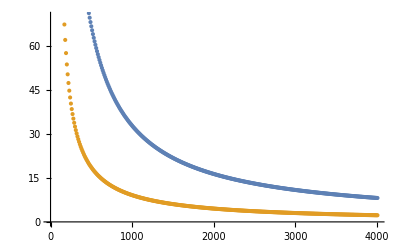

```mathematica
ListPlot[{condZRCperf[[1]],condZRCperf[[3]]}]
```

```mathematica
optionsZRC={AspectRatio->1,FrameLabel->{Style["T (K)",15],Style["κ (W/m/K)",15]},FrameTicksStyle->15,Frame->True,ImageSize->450,PlotLegends->Placed[SwatchLegend[{Style["1MBTE-LD - 0 K volume (NO ZP corrections)",15],Style["1MBTE-LD - MP volume",15]}],{0.53,0.87}],PlotLabel->Style["ZrC bulk phonon conductivity with isotope scattering",15],PlotStyle->Thickness[0.007],PlotRange->{{0,3000},{0,150}},PlotTheme->"Scientific"};
```

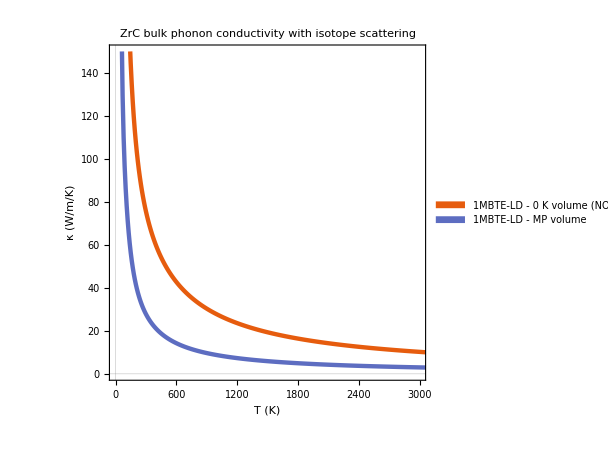

```mathematica
zrcCondp1=Show[{ListLinePlot[condZRCperf[[1]],Evaluate[optionsZRC]]}];
zrcCondp2=Show[{ListLinePlot[{condZRCperf[[1]],condZRCperf[[3]]},Evaluate[optionsZRC]]}];
zrcCondp3=Show[{ListLinePlot[condZRCiso[[1]],Evaluate[optionsZRC]]}];
zrcCondp4=Show[{ListLinePlot[{condZRCiso[[1]],condZRCiso[[3]]},Evaluate[optionsZRC]]}]
```

```mathematica
(*100 7 0.1890541501E+03-0.1164035453E-01-0.4105335240E-01 0.1142042854E-01 0.1890553910E+03 0.1138543408E-01 0.3943374721E-01-0.2707150749E-01 0.1890507718E+03*)
SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/Conductivity_ZrC/OUT_ZrC_CS/"];
fileCS={"kappa-T-0", "kappa-T-300", "kappa-T-1000","kappa-T-1500","kappa-T-2500" ,"kappa-T-3800"};
csCond=Table[ReadList[fileCS[[i]],{Number, Number,Number, Number,Number, Number,Number,Number, Number,Number,Number}],{i,1,fileCS//Length}];
```

```mathematica
condCS=Table[Transpose@{Transpose[csCond[[i]]][[1]],Transpose[csCond[[i]]][[3]]},{i,1,fileCS//Length}];
```

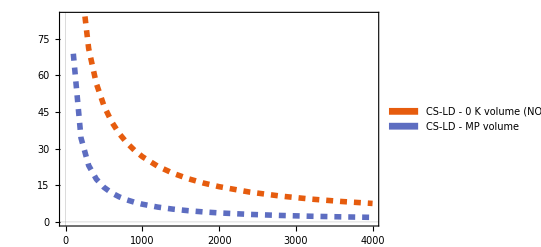

```mathematica
csOptions={PlotTheme->"Scientific",PlotStyle->Directive[Dashed,Thickness[0.01]],PlotLegends->Placed[SwatchLegend[{Style["CS-LD - 0 K volume (NO ZP corrections)",15],Style["CS-LD - MP volume",15]}],{0.49,0.75}]};
zrcCondp5=ListLinePlot[{condCS[[1]],condCS[[6]]},Evaluate[csOptions]]
Show[{zrcCondp4,zrcCondp5}]
```

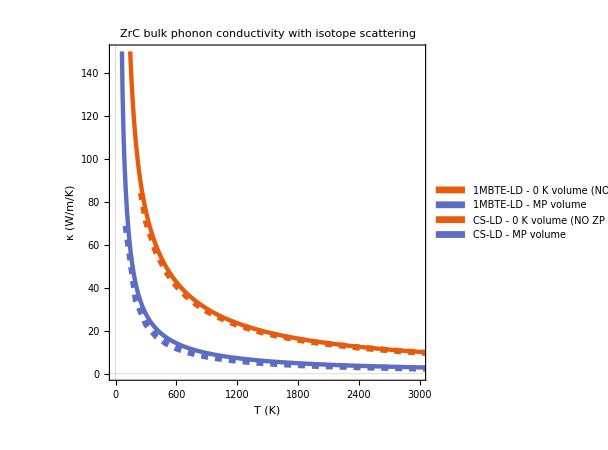

```mathematica
kappael0={{10,0.1879668857931059},{300,5.0080514187339995},{760,8.576071758295253},{1900,17.759917867965825},{2500,19.264609934131553},{3200,19.171546044534168},{3800,17.22143257139503}};
kappaelmp={{10,0.13221214314524193},{300,4.662273631604339},{760,8.166648670778342},{1900,16.348797468871595},{2500,17.43566843521913},{3200,17.110245005709807},{3800,15.250776362908358}};
```

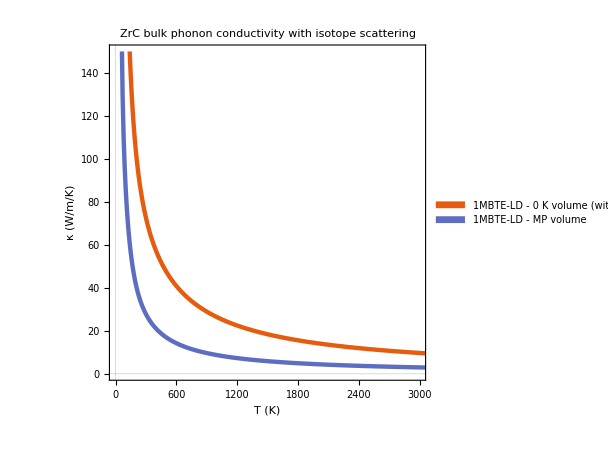

```mathematica
ListLinePlot[{condZRCiso[[2]],condZRCiso[[3]]},Evaluate[optionsZRC]]
```

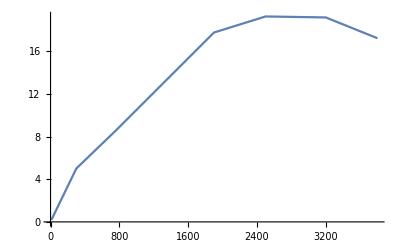

```mathematica
ListLinePlot@kappael0
```

401

7.54182-68.2197/x-0.0855023 x-8.38275×10^-6 x^2+7.09353×10^-14 x^4+0.014076 x Log[x]

-0.377583+0.089466 x+0.0000204881 x^2-5.61057×10^-9 x^3+5.51685×10^-13 x^4-0.0135796 x Log[x]

InterpolatingFunction[{{10., 3800.}}, <>]

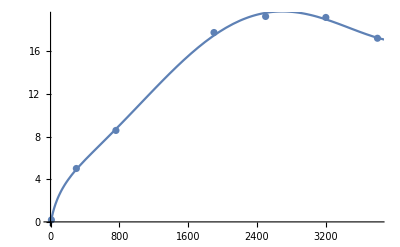

```mathematica
condZRCiso[[2]]//Length

Fit[kappael0,{1,x,x*x,x*x*x*x,1/x,x*Log[x]},x]
kfit=Fit[kappael0,{1,x,x*x,x*x*x,x*x*x*x,x*Log[x]},x]
kinter=Interpolation[kappael0]
Show[{ListPlot@kappael0,Plot[{kfit},{x,0,4000}]}]
```

```mathematica
kfit
```

kfit

```mathematica
kelZRC=Table[{10i,kfit/.x->10i},{i,1,401}];
ktotalZRC0=Table[{10i,condZRCiso[[2]][[i]][[2]]+kfit/.x->10i},{i,1,401}];
ktotalZRCmp=Table[{10i,condZRCiso[[3]][[i]][[2]]+kfit/.x->10i},{i,1,401}];
ktotalZRC0bmf01=Table[{10i,condZRC0all[[5]][[i]][[2]]+kfit/.x->10i},{i,1,401}];
```

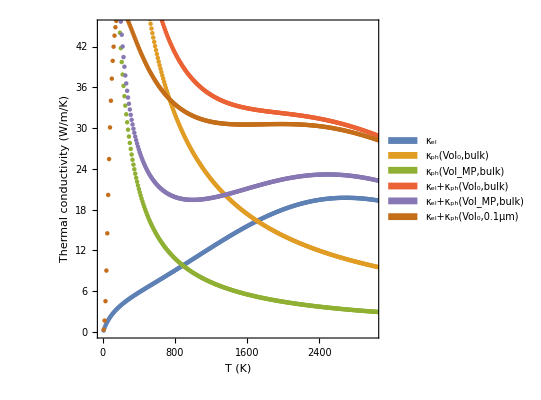

```mathematica
ListPlot[{kelZRC,condZRCiso[[2]],condZRCiso[[3]],ktotalZRC0,ktotalZRCmp,ktotalZRC0bmf01},PlotRange->{{0,3000},{0,45}},PlotStyle->PointSize[0.008],PlotLegends->SwatchLegend[{"κ_el","κ_ph(Vol_0,bulk)","κ_ph(Vol_MP,bulk)","κ_el+κ_ph(Vol_0,bulk)","κ_el+κ_ph(Vol_MP,bulk)","κ_el+κ_ph(Vol_0,0.1μm)"}],Frame->True,FrameTicks->True,AspectRatio->1,FrameLabel->{"T (K)","Thermal conductivity (W/m/K)"}]
```

```mathematica
SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/Conductivity_ZrC/ZrC_kappaPh_RESULTS/"];
file0all={"0_noZP/BULK/ISO/t_kappa_31.dat","0_noZP/100bmf/ISO/t_kappa_31.dat", "0_noZP/10bmf/ISO/t_kappa_31.dat", "0_noZP/1bmf/ISO/t_kappa_31.dat","0_noZP/0.1bmf/ISO/t_kappa_31.dat"};
zrc0all=Table[ReadList[file0all[[i]],{Number, Number,Number, Number,Number, Number,Number}],{i,1,file0all//Length}];
```

```mathematica
condZRC0all=Table[Transpose[{Transpose[zrc0all[[i]]][[1]],Transpose[zrc0all[[i]]][[2]]}],{i,1,5,1}];
```

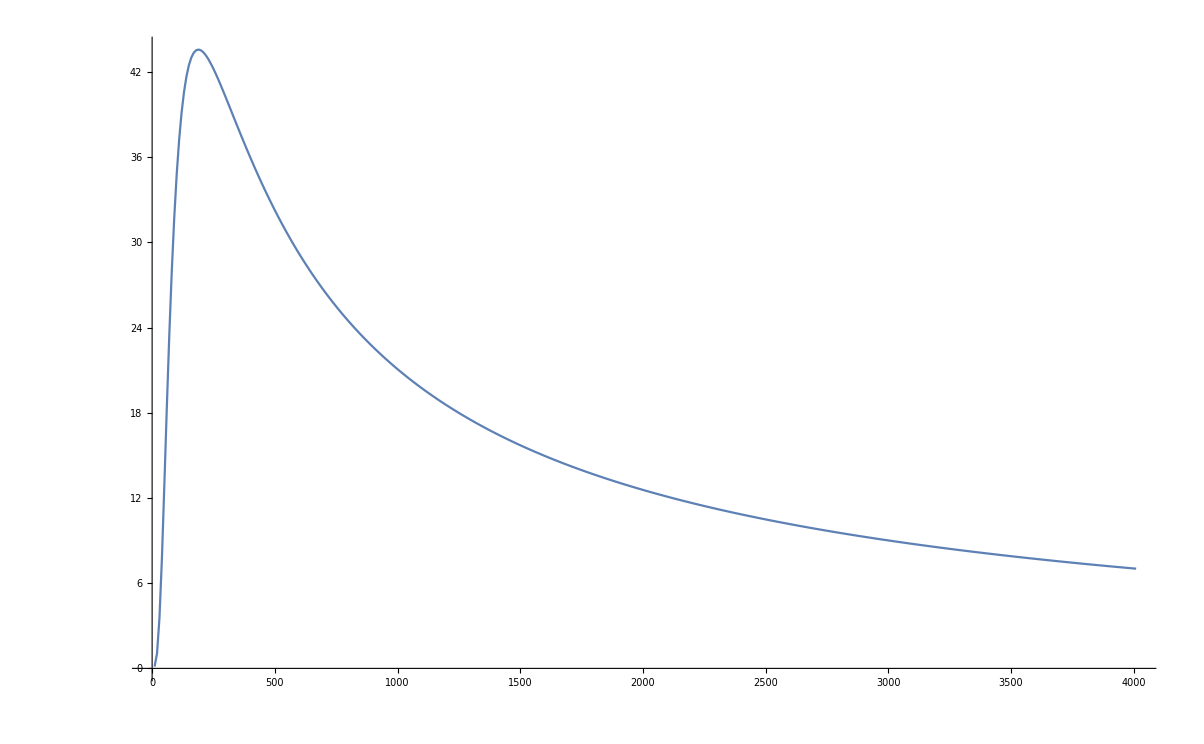

```mathematica
ListLinePlot[condZRC0all[[5]]]
```